## Tadpole dynamics

We lookout for self-tuning solutions in the presence of a tadpole.

```mathematica
SetDirectory[NotebookDirectory[]];
Get["tadpole_friedmann_eqs.m"];
```

### I. Review: The Friedmann equations

We review the Friedmann equations derived in tadpole_cosmology.nb using the xAct packages. The Friedmann constraint is given by...

```mathematica
Feq==0/.κ->ℳ^2/2
```

1/2 (-Λ+Q[1/2 φ'[t]^2]+V[φ[t]]-ρ[t]-λ^3 φ[t]+3 H[t]^2 (ℳ^2+F[φ[t]]+M φ[t])-Q'[1/2 φ'[t]^2] φ'[t]^2+3 H[t] φ'[t] (M+F'[φ[t]]-φ'[t]^2 G^(0,1)[φ[t],1/2 φ'[t]^2])+φ'[t]^2 G^(1,0)[φ[t],1/2 φ'[t]^2])==0

The Hubble equation is given by...

```mathematica
Heq=Feq/.Solve[Peq==0,Q[φ'[t]^2/2]][[1]]/.κ->ℳ^2/2//Simplify;Heq==0
```

1/2 (-P[t]-ρ[t]-2 ℳ^2 H'[t]-2 F[φ[t]] H'[t]-2 M φ[t] H'[t]+M H[t] φ'[t]+H[t] F'[φ[t]] φ'[t]-Q'[1/2 φ'[t]^2] φ'[t]^2-φ'[t]^2 F''[φ[t]]-M φ''[t]-F'[φ[t]] φ''[t]-3 H[t] φ'[t]^3 G^(0,1)[φ[t],1/2 φ'[t]^2]+φ'[t]^2 φ''[t] G^(0,1)[φ[t],1/2 φ'[t]^2]+2 φ'[t]^2 G^(1,0)[φ[t],1/2 φ'[t]^2])==0

The scalar field equation is given by...

```mathematica
Seq==0/.κ->ℳ^2/2
```

-λ^3+V'[φ[t]]-Q'[1/2 φ'[t]^2] φ''[t]-φ'[t]^2 Q''[1/2 φ'[t]^2] φ''[t]+H[t]^2 (6 M+6 F'[φ[t]]-9 φ'[t]^2 G^(0,1)[φ[t],1/2 φ'[t]^2])+3 H'[t] (M+F'[φ[t]]-φ'[t]^2 G^(0,1)[φ[t],1/2 φ'[t]^2])+2 φ''[t] G^(1,0)[φ[t],1/2 φ'[t]^2]+φ'[t]^2 φ''[t] G^(1,1)[φ[t],1/2 φ'[t]^2]-3 H[t] φ'[t] (Q'[1/2 φ'[t]^2]+φ''[t] (2 G^(0,1)[φ[t],1/2 φ'[t]^2]+φ'[t]^2 G^(0,2)[φ[t],1/2 φ'[t]^2])-2 G^(1,0)[φ[t],1/2 φ'[t]^2]+φ'[t]^2 G^(1,1)[φ[t],1/2 φ'[t]^2])+φ'[t]^2 G^(2,0)[φ[t],1/2 φ'[t]^2]==0

For our purposes in this notebook, we consider the braiding potential to depend only on the kinetic term. We simplify the field equation as follows...

```mathematica
SimpG=G->Function[{a,b},G[b]];

FeqTC=3 H[t]^2(2κ+F[φ[t]]+M φ[t])==(3Hsq (2κ+F[φ[t]]+M φ[t])/.Solve[Feq==0/.SimpG/.H[t]^2->Hsq,Hsq][[1]]//Simplify)/.κ->ℳ^2/2;
HeqTC=-2H'[t](2κ+F[φ[t]]+M φ[t])==Collect[(-2H'[t](2κ+F[φ[t]]+M φ[t])/.Solve[Heq==0/.SimpG,H'[t]][[1]]//Simplify),{φ''[t],φ'[t]},Simplify]/.κ->ℳ^2/2;
SeqTC=Collect[-Seq/.SimpG//Simplify,{φ''[t],φ'[t]},Simplify]==0/.κ->ℳ^2/2;

FeqTC
HeqTC
SeqTC
```

3 H[t]^2 (ℳ^2+F[φ[t]]+M φ[t])==Λ-Q[1/2 φ'[t]^2]-V[φ[t]]+ρ[t]+λ^3 φ[t]-3 M H[t] φ'[t]-3 H[t] F'[φ[t]] φ'[t]+Q'[1/2 φ'[t]^2] φ'[t]^2+3 H[t] G'[1/2 φ'[t]^2] φ'[t]^3

-2 (ℳ^2+F[φ[t]]+M φ[t]) H'[t]==P[t]+ρ[t]-H[t] (M+F'[φ[t]]) φ'[t]+3 H[t] G'[1/2 φ'[t]^2] φ'[t]^3+φ'[t]^2 (Q'[1/2 φ'[t]^2]+F''[φ[t]])+(M+F'[φ[t]]-G'[1/2 φ'[t]^2] φ'[t]^2) φ''[t]

λ^3-6 H[t]^2 (M+F'[φ[t]])-3 (M+F'[φ[t]]) H'[t]-V'[φ[t]]+3 H[t] Q'[1/2 φ'[t]^2] φ'[t]+3 G'[1/2 φ'[t]^2] (3 H[t]^2+H'[t]) φ'[t]^2+(Q'[1/2 φ'[t]^2]+6 H[t] G'[1/2 φ'[t]^2] φ'[t]+3 H[t] φ'[t]^3 G''[1/2 φ'[t]^2]+φ'[t]^2 Q''[1/2 φ'[t]^2]) φ''[t]==0

We proceed from this.

### II. Degenerate field equations: Fugue in B Flat

Provided that F(x)=V(x)=0, it can be shown that the field equations are degenerate (on a Minkowski background) if:

```mathematica
BFlat=(2x Q'[x])/(M-2x G'[x])==λ^3/(Q'[x]+2x Q''[x]);
```

This is nearly satisfied for example by the Galileon model (M=0)...

```mathematica
NearlyBbm={Q->Function[x,ϵ x],G->Function[x,-ϵ^2/κ^3 x]};
BFlat/.M->0/.NearlyBbm//Simplify
```

(κ^3-λ^3)/ϵ==0

For κ=λ, there exists an exact Minkowski solution (H=0). On this background, the scalar field behaves as...

```mathematica
DegenerateFV={F->Function[x,0],V->Function[x,0]};
OnShell={ρ->Function[t,0],P->Function[t,0],H->Function[t,0]};

FeqTC/.M->0/.DegenerateFV/.NearlyBbm/.κ->λ/.OnShell//Simplify
HeqTC/.M->0/.DegenerateFV/.NearlyBbm/.κ->λ/.OnShell//Simplify
SeqTC/.M->0/.DegenerateFV/.NearlyBbm.κ->λ/.OnShell//Simplify
```

2 Λ+2 λ^3 φ[t]+ϵ φ'[t]^2==0

(ϵ φ'[t] (λ^3+ϵ φ''[t]))/λ==0

λ^3+(Q'[1/2 φ'[t]^2]+φ'[t]^2 Q''[1/2 φ'[t]^2]) φ''[t]==0

This confirms that the Hubble and scalar field equations do reduce to the same equation, i.e., degenerate. The scalar field is then solved by...

```mathematica
φBbm=DSolve[SeqTC/.M->0/.DegenerateFV/.NearlyBbm/.κ->λ/.OnShell//Simplify,φ,t][[1]];
φ[t]==(φ[t]/.φBbm)
```

φ[t]==-(t^2 λ^3)/(2 ϵ)+C[1]+t C[2]

The constants c_i (determining the scalar field’s initial conditions) enter the Friedmann constraint to cancel out Λ...

```mathematica
FeqTC/.M->0/.DegenerateFV/.NearlyBbm/.κ->λ/.OnShell/.φBbm//Simplify
```

2 Λ+2 λ^3 C[1]+ϵ C[2]^2==0

This is known as the B Flat minor (Bbm) solution.

### III. Nondegenerate models

We explore various ways to break the degeneracy in the field equations.

#### A. κ≠λ

We recall the nearly Bbm potentials...

```mathematica
NearlyBbm
```

{Q→Function[x,ϵ x],G→Function[x,-(ϵ^2 x)/κ^3]}

We define dimensionless variables so the field equations become...

```mathematica
$Assumptions=λ≠0&&ϵ>0;

Vacuum={ρ->Function[t,0],P->Function[t,0]};
GoDimless={κ->λ/α,ℳ->λ Δ,Λ->Γ λ^4,H[t]->λ h[τ],H'[t]->λ^2 h'[τ],φ[t]->λ ψ[τ],φ'[t]->λ^2 ψ'[τ],φ''[t]->λ^3 ψ''[τ]};

FeqTCdb1=3 Δ^2 h[τ]^2==(3 Δ^2 hsq/.Solve[FeqTC/.M->0/.DegenerateFV/.NearlyBbm/.Vacuum/.GoDimless/.h[τ]^2->hsq,hsq][[1]]//Simplify);
HeqTCdb1=-2 Δ^2 h'[τ]==(-2 Δ^2 h'[τ]/.Solve[HeqTC/.M->0/.DegenerateFV/.NearlyBbm/.Vacuum/.GoDimless,h'[τ]][[1]]);
SeqTCdb1=0==ψ''[τ](ϵ-6 ϵ^2 α^3 h[τ]ψ'[τ])-(ψ''[τ](ϵ-6 ϵ^2 α^3 h[τ]ψ'[τ])/.Solve[SeqTC/.M->0/.DegenerateFV/.NearlyBbm/.Vacuum/.GoDimless//Simplify,ψ''[τ]][[1]]//Simplify);

FeqTCdb1
HeqTCdb1
SeqTCdb1
```

3 Δ^2 h[τ]^2==Γ+ψ[τ]+1/2 ϵ ψ'[τ]^2-3 α^3 ϵ^2 h[τ] ψ'[τ]^3

-2 Δ^2 h'[τ]==ϵ ψ'[τ]^2-3 α^3 ϵ^2 h[τ] ψ'[τ]^3+α^3 ϵ^2 ψ'[τ]^2 ψ''[τ]

0==1+3 ϵ h[τ] ψ'[τ]-9 α^3 ϵ^2 h[τ]^2 ψ'[τ]^2-3 α^3 ϵ^2 h'[τ] ψ'[τ]^2+(ϵ-6 α^3 ϵ^2 h[τ] ψ'[τ]) ψ''[τ]

There is a large time asymptotic solution to this system of the form...

```mathematica
Ord=5;
AsympSoldb1={ψ->Function[τ,τ^2 Sum[φ[i] τ^-i,{i,0,Ord}]],h->Function[τ,τ^-1 Sum[𝒽[i] τ^-i,{i,0,Ord}]]};
```

Expanding the field equations order by order, we get...

```mathematica
FeqTCdb1series=Series[-(FeqTCdb1[[1]]-FeqTCdb1[[2]])/.AsympSoldb1,{τ,∞,Ord-2}];
HeqTCdb1series=Series[-1/4(HeqTCdb1[[1]]-HeqTCdb1[[2]])/.AsympSoldb1,{τ,∞,Ord-2}];
SeqTCdb1series=Series[-(SeqTCdb1[[1]]-SeqTCdb1[[2]])/.AsympSoldb1,{τ,∞,Ord-2}];

FeqTCdb1eqns=Table[SeriesCoefficient[FeqTCdb1series,n]==0,{n,-2,Ord-2}];
HeqTCdb1eqns=Table[SeriesCoefficient[HeqTCdb1series,n]==0,{n,-2,Ord-2}];
SeqTCdb1eqns=Table[SeriesCoefficient[SeqTCdb1series,n]==0,{n,-2,Ord-2}];

FeqTCdb1eqns
HeqTCdb1eqns
SeqTCdb1eqns
```

{φ[0]+2 ϵ φ[0]^2-24 α^3 ϵ^2 𝒽[0] φ[0]^3==0,φ[1]+2 ϵ φ[0] φ[1]-3 α^3 ϵ^2 (8 𝒽[1] φ[0]^3+12 𝒽[0] φ[0]^2 φ[1])==0,Γ+1/2 ϵ φ[1]^2-3 α^3 ϵ^2 (8 𝒽[2] φ[0]^3+12 𝒽[1] φ[0]^2 φ[1]+6 𝒽[0] φ[0] φ[1]^2)+φ[2]==0,φ[3]-2 ϵ φ[0] φ[3]-3 α^3 ϵ^2 (8 𝒽[3] φ[0]^3+12 𝒽[2] φ[0]^2 φ[1]+6 𝒽[1] φ[0] φ[1]^2+𝒽[0] φ[1]^3-12 𝒽[0] φ[0]^2 φ[3])==0,-3 Δ^2 𝒽[0]^2+φ[4]-ϵ (φ[1] φ[3]+4 φ[0] φ[4])-3 α^3 ϵ^2 (8 𝒽[4] φ[0]^3+12 𝒽[3] φ[0]^2 φ[1]+6 𝒽[2] φ[0] φ[1]^2+𝒽[1] φ[1]^3-12 𝒽[1] φ[0]^2 φ[3]-12 𝒽[0] φ[0] φ[1] φ[3]-24 𝒽[0] φ[0]^2 φ[4])==0,-6 Δ^2 𝒽[0] 𝒽[1]+φ[5]-2 ϵ (φ[1] φ[4]+3 φ[0] φ[5])-3 α^3 ϵ^2 (8 𝒽[5] φ[0]^3+12 𝒽[4] φ[0]^2 φ[1]+6 𝒽[3] φ[0] φ[1]^2+𝒽[2] φ[1]^3-12 𝒽[2] φ[0]^2 φ[3]-12 𝒽[1] φ[0] φ[1] φ[3]-3 𝒽[0] φ[1]^2 φ[3]-24 𝒽[1] φ[0]^2 φ[4]-24 𝒽[0] φ[0] φ[1] φ[4]-36 𝒽[0] φ[0]^2 φ[5])==0}

{ϵ φ[0]^2+2 α^3 ϵ^2 φ[0]^3-6 α^3 ϵ^2 𝒽[0] φ[0]^3==0,-6 α^3 ϵ^2 𝒽[1] φ[0]^3+ϵ φ[0] φ[1]+2 α^3 ϵ^2 φ[0]^2 φ[1]-9 α^3 ϵ^2 𝒽[0] φ[0]^2 φ[1]==0,1/4 (ϵ φ[1]^2+2 α^3 ϵ^2 φ[0] φ[1]^2-3 α^3 ϵ^2 (8 𝒽[2] φ[0]^3+12 𝒽[1] φ[0]^2 φ[1]+6 𝒽[0] φ[0] φ[1]^2))==0,1/4 (-4 ϵ φ[0] φ[3]-3 α^3 ϵ^2 (8 𝒽[3] φ[0]^3+12 𝒽[2] φ[0]^2 φ[1]+6 𝒽[1] φ[0] φ[1]^2+𝒽[0] φ[1]^3-12 𝒽[0] φ[0]^2 φ[3]))==0,1/4 (-2 Δ^2 𝒽[0]+ϵ (-2 φ[1] φ[3]-8 φ[0] φ[4])+4 α^3 ϵ^2 (φ[0] φ[1] φ[3]+2 φ[0]^2 φ[4])-3 α^3 ϵ^2 (8 𝒽[4] φ[0]^3+12 𝒽[3] φ[0]^2 φ[1]+6 𝒽[2] φ[0] φ[1]^2+𝒽[1] φ[1]^3-12 𝒽[1] φ[0]^2 φ[3]-12 𝒽[0] φ[0] φ[1] φ[3]-24 𝒽[0] φ[0]^2 φ[4]))==0,1/4 (-4 Δ^2 𝒽[1]+ϵ (-4 φ[1] φ[4]-12 φ[0] φ[5])+2 α^3 ϵ^2 (φ[1]^2 φ[3]+8 φ[0] φ[1] φ[4]+12 φ[0]^2 φ[5])-3 α^3 ϵ^2 (8 𝒽[5] φ[0]^3+12 𝒽[4] φ[0]^2 φ[1]+6 𝒽[3] φ[0] φ[1]^2+𝒽[2] φ[1]^3-12 𝒽[2] φ[0]^2 φ[3]-12 𝒽[1] φ[0] φ[1] φ[3]-3 𝒽[0] φ[1]^2 φ[3]-24 𝒽[1] φ[0]^2 φ[4]-24 𝒽[0] φ[0] φ[1] φ[4]-36 𝒽[0] φ[0]^2 φ[5]))==0}

{True,True,1+2 ϵ φ[0]+6 ϵ 𝒽[0] φ[0]-12 α^3 ϵ^2 𝒽[0] φ[0]^2-36 α^3 ϵ^2 𝒽[0]^2 φ[0]^2==0,-3 (-2 ϵ 𝒽[1] φ[0]+24 α^3 ϵ^2 𝒽[0] 𝒽[1] φ[0]^2-ϵ 𝒽[0] φ[1]+12 α^3 ϵ^2 𝒽[0]^2 φ[0] φ[1])==0,3 ϵ (2 𝒽[2] φ[0]+𝒽[1] φ[1])-12 α^3 ϵ^2 φ[0] (2 𝒽[2] φ[0]+𝒽[1] φ[1])+3 α^3 ϵ^2 (12 𝒽[2] φ[0]^2+8 𝒽[1] φ[0] φ[1]+𝒽[0] φ[1]^2)-9 α^3 ϵ^2 (4 (𝒽[1]^2+2 𝒽[0] 𝒽[2]) φ[0]^2+8 𝒽[0] 𝒽[1] φ[0] φ[1]+𝒽[0]^2 φ[1]^2)==0,2 (ϵ-12 α^3 ϵ^2 𝒽[0] φ[0]) φ[3]+3 ϵ (2 𝒽[3] φ[0]+𝒽[2] φ[1]-𝒽[0] φ[3])-12 α^3 ϵ^2 φ[0] (2 𝒽[3] φ[0]+𝒽[2] φ[1]-𝒽[0] φ[3])+6 α^3 ϵ^2 (8 𝒽[3] φ[0]^2+6 𝒽[2] φ[0] φ[1]+𝒽[1] φ[1]^2-2 𝒽[0] φ[0] φ[3])-9 α^3 ϵ^2 (4 (2 𝒽[1] 𝒽[2]+2 𝒽[0] 𝒽[3]) φ[0]^2+4 (𝒽[1]^2+2 𝒽[0] 𝒽[2]) φ[0] φ[1]+2 𝒽[0] 𝒽[1] φ[1]^2-4 𝒽[0]^2 φ[0] φ[3])==0}

At the leading order, we obtain the asymptotic well-tempered Minkowski state...

```mathematica
φ𝒽0TCdb1=Solve[{FeqTCdb1eqns[[1]],HeqTCdb1eqns[[1]]},{𝒽[0],φ[0]}]//Quiet//Simplify;φ𝒽0TCdb1
```

{{φ[0]→0},{𝒽[0]→(1+2 α^3-√(1+8 α^3))/(6 α^3),φ[0]→-(1+√(1+8 α^3))/(8 α^3 ϵ)},{𝒽[0]→(1+2 α^3+√(1+8 α^3))/(6 α^3),φ[0]→(-1+√(1+8 α^3))/(8 α^3 ϵ)}}

At the next orders, we have...

```mathematica
φ𝒽1TCdb1=Solve[{FeqTCdb1eqns[[2]],HeqTCdb1eqns[[2]]},{𝒽[1],φ[1]}]//Simplify;
φ𝒽2TCdb1=Solve[{FeqTCdb1eqns[[3]],HeqTCdb1eqns[[3]]},{𝒽[2],φ[2]}]//Simplify;
φ𝒽3TCdb1=Solve[{FeqTCdb1eqns[[4]],HeqTCdb1eqns[[4]]},{𝒽[3],φ[3]}]//Simplify;
φ𝒽4TCdb1=Solve[{FeqTCdb1eqns[[5]],HeqTCdb1eqns[[5]]},{𝒽[4],φ[4]}]//Simplify;

φ𝒽1TCdb1
φ𝒽2TCdb1/.φ𝒽1TCdb1
φ𝒽3TCdb1/.φ𝒽2TCdb1[[1]]/.φ𝒽1TCdb1[[1]]/.φ𝒽0TCdb1[[2]]//Simplify
φ𝒽4TCdb1/.φ𝒽3TCdb1[[1]]/.φ𝒽2TCdb1[[1]]/.φ𝒽1TCdb1[[1]]/.φ𝒽0TCdb1[[2]]//Simplify
```

{{𝒽[1]→0,φ[1]→0}}

{{{𝒽[2]→0,φ[2]→-Γ}}}

{{𝒽[3]→0,φ[3]→0}}

{{𝒽[4]→(128 α^3 (-1-2 α^3+√(1+8 α^3)) (-1+4 α^3+√(1+8 α^3)) Δ^2 ϵ)/(27 (1+√(1+8 α^3))^4),φ[4]→(2 (-1-4 α^3+2 α^6+√(1+8 α^3)) Δ^2)/(9 α^3 (1+√(1+8 α^3)))}}

#### B. Mφ R

We prepare the Friedmann equations with conformal coupling...

```mathematica
$Assumptions=λ≠0&&ϵ>0&&m≥0;

Vacuum={ρ->Function[t,0],P->Function[t,0]};
GoDimless={κ->λ/α,ℳ->λ Δ,Λ->Γ λ^4,H[t]->λ h[τ],H'[t]->λ^2 h'[τ],φ[t]->λ ψ[τ],φ'[t]->λ^2 ψ'[τ],φ''[t]->λ^3 ψ''[τ]};
db3={F->Function[x,0],V->Function[x,0]};

FeqTCdb3=3(Δ^2+Μ ψ[τ])h[τ]^2==(3(Δ^2+Μ ψ[τ])hsq/.Solve[FeqTC/.db3/.(NearlyBbm/.κ->λ)/.Vacuum/.GoDimless/.M->λ Μ/.h[τ]^2->hsq,hsq][[1]]//Simplify);
HeqTCdb3=-2(Δ^2+Μ ψ[τ])h'[τ]==(-2(Δ^2+Μ ψ[τ])h'[τ]/.Solve[HeqTC/.db3/.(NearlyBbm/.κ->λ)/.Vacuum/.GoDimless/.M->λ Μ,h'[τ]][[1]]);
SeqTCdb3=0==ψ''[τ](ϵ-6 ϵ^2 h[τ]ψ'[τ])-(ψ''[τ](ϵ-6 ϵ^2 h[τ]ψ'[τ])/.Solve[SeqTC/.db3/.(NearlyBbm/.κ->λ)/.Vacuum/.GoDimless/.M->λ Μ//Simplify,ψ''[τ]][[1]]//Simplify);

FeqTCdb3
HeqTCdb3
SeqTCdb3
```

3 h[τ]^2 (Δ^2+Μ ψ[τ])==Γ+ψ[τ]+1/2 ϵ ψ'[τ]^2-3 h[τ] ψ'[τ] (Μ+ϵ^2 ψ'[τ]^2)

-2 (Δ^2+Μ ψ[τ]) h'[τ]==-Μ h[τ] ψ'[τ]+ϵ ψ'[τ]^2-3 ϵ^2 h[τ] ψ'[τ]^3+Μ ψ''[τ]+ϵ^2 ψ'[τ]^2 ψ''[τ]

0==1+3 ϵ h[τ] ψ'[τ]-3 h'[τ] (Μ+ϵ^2 ψ'[τ]^2)-h[τ]^2 (6 Μ+9 ϵ^2 ψ'[τ]^2)+(ϵ-6 ϵ^2 h[τ] ψ'[τ]) ψ''[τ]

This system admits a power law expansion of the form...

```mathematica
Ord=5;
AsympSoldb3={ψ->Function[τ,τ^2 Sum[φ[i] τ^-i,{i,0,Ord}]],h->Function[τ,τ^-1 Sum[𝒽[i] τ^-i,{i,0,Ord}]]};

FeqTCdb3series=Series[-(FeqTCdb3[[1]]-FeqTCdb3[[2]])/.AsympSoldb3,{τ,∞,Ord-2}];
HeqTCdb3series=Series[-1/4(HeqTCdb3[[1]]-HeqTCdb3[[2]])/.AsympSoldb3,{τ,∞,Ord-2}];
SeqTCdb3series=Series[-(SeqTCdb3[[1]]-SeqTCdb3[[2]])/.AsympSoldb3,{τ,∞,Ord-2}];

FeqTCdb3eqns=Table[SeriesCoefficient[FeqTCdb3series,n]==0,{n,-2,Ord-2}];
HeqTCdb3eqns=Table[SeriesCoefficient[HeqTCdb3series,n]==0,{n,-2,Ord-2}];
SeqTCdb3eqns=Table[SeriesCoefficient[SeqTCdb3series,n]==0,{n,-2,Ord-2}];

FeqTCdb3eqns
HeqTCdb3eqns
SeqTCdb3eqns
```

{φ[0]+2 ϵ φ[0]^2-24 ϵ^2 𝒽[0] φ[0]^3==0,-24 ϵ^2 𝒽[1] φ[0]^3+φ[1]+2 ϵ φ[0] φ[1]-36 ϵ^2 𝒽[0] φ[0]^2 φ[1]==0,Γ-3 Μ 𝒽[0]^2 φ[0]+1/2 ϵ φ[1]^2-6 (Μ 𝒽[0] φ[0]+4 ϵ^2 𝒽[2] φ[0]^3+6 ϵ^2 𝒽[1] φ[0]^2 φ[1]+3 ϵ^2 𝒽[0] φ[0] φ[1]^2)+φ[2]==0,-6 Μ 𝒽[1] φ[0]-6 Μ 𝒽[0] 𝒽[1] φ[0]-24 ϵ^2 𝒽[3] φ[0]^3-3 Μ 𝒽[0] φ[1]-3 Μ 𝒽[0]^2 φ[1]-36 ϵ^2 𝒽[2] φ[0]^2 φ[1]-18 ϵ^2 𝒽[1] φ[0] φ[1]^2-3 ϵ^2 𝒽[0] φ[1]^3+φ[3]-2 ϵ φ[0] φ[3]+36 ϵ^2 𝒽[0] φ[0]^2 φ[3]==0,-3 (Μ (𝒽[1]^2+2 𝒽[0] 𝒽[2]) φ[0]+2 Μ 𝒽[0] 𝒽[1] φ[1]+𝒽[0]^2 (Δ^2+Μ φ[2]))+φ[4]-ϵ (φ[1] φ[3]+4 φ[0] φ[4])-3 (2 Μ 𝒽[2] φ[0]+8 ϵ^2 𝒽[4] φ[0]^3+Μ 𝒽[1] φ[1]+12 ϵ^2 𝒽[3] φ[0]^2 φ[1]+6 ϵ^2 𝒽[2] φ[0] φ[1]^2+ϵ^2 𝒽[1] φ[1]^3-12 ϵ^2 𝒽[1] φ[0]^2 φ[3]-12 ϵ^2 𝒽[0] φ[0] φ[1] φ[3]-24 ϵ^2 𝒽[0] φ[0]^2 φ[4])==0,-3 (Μ (2 𝒽[1] 𝒽[2]+2 𝒽[0] 𝒽[3]) φ[0]+Μ (𝒽[1]^2+2 𝒽[0] 𝒽[2]) φ[1]+2 𝒽[0] 𝒽[1] (Δ^2+Μ φ[2])+Μ 𝒽[0]^2 φ[3])+φ[5]-2 ϵ (φ[1] φ[4]+3 φ[0] φ[5])-3 (2 Μ 𝒽[3] φ[0]+8 ϵ^2 𝒽[5] φ[0]^3+Μ 𝒽[2] φ[1]+12 ϵ^2 𝒽[4] φ[0]^2 φ[1]+6 ϵ^2 𝒽[3] φ[0] φ[1]^2+ϵ^2 𝒽[2] φ[1]^3-Μ 𝒽[0] φ[3]-12 ϵ^2 𝒽[2] φ[0]^2 φ[3]-12 ϵ^2 𝒽[1] φ[0] φ[1] φ[3]-3 ϵ^2 𝒽[0] φ[1]^2 φ[3]-24 ϵ^2 𝒽[1] φ[0]^2 φ[4]-24 ϵ^2 𝒽[0] φ[0] φ[1] φ[4]-36 ϵ^2 𝒽[0] φ[0]^2 φ[5])==0}

{ϵ φ[0]^2+2 ϵ^2 φ[0]^3-6 ϵ^2 𝒽[0] φ[0]^3==0,-6 ϵ^2 𝒽[1] φ[0]^3+ϵ φ[0] φ[1]+2 ϵ^2 φ[0]^2 φ[1]-9 ϵ^2 𝒽[0] φ[0]^2 φ[1]==0,1/4 (2 Μ φ[0]-4 Μ 𝒽[0] φ[0]+ϵ φ[1]^2+2 ϵ^2 φ[0] φ[1]^2-3 ϵ^2 (8 𝒽[2] φ[0]^3+12 𝒽[1] φ[0]^2 φ[1]+6 𝒽[0] φ[0] φ[1]^2))==0,1/4 (-6 Μ 𝒽[1] φ[0]-24 ϵ^2 𝒽[3] φ[0]^3-3 Μ 𝒽[0] φ[1]-36 ϵ^2 𝒽[2] φ[0]^2 φ[1]-18 ϵ^2 𝒽[1] φ[0] φ[1]^2-3 ϵ^2 𝒽[0] φ[1]^3-4 ϵ φ[0] φ[3]+36 ϵ^2 𝒽[0] φ[0]^2 φ[3])==0,1/4 (Μ (-2 𝒽[2] φ[0]-𝒽[1] φ[1])+2 (-3 Μ 𝒽[2] φ[0]-2 Μ 𝒽[1] φ[1]-𝒽[0] (Δ^2+Μ φ[2]))+ϵ (-2 φ[1] φ[3]-8 φ[0] φ[4])+4 ϵ^2 (φ[0] φ[1] φ[3]+2 φ[0]^2 φ[4])-3 ϵ^2 (8 𝒽[4] φ[0]^3+12 𝒽[3] φ[0]^2 φ[1]+6 𝒽[2] φ[0] φ[1]^2+𝒽[1] φ[1]^3-12 𝒽[1] φ[0]^2 φ[3]-12 𝒽[0] φ[0] φ[1] φ[3]-24 𝒽[0] φ[0]^2 φ[4]))==0,1/4 (2 Μ φ[3]+Μ (-2 𝒽[3] φ[0]-𝒽[2] φ[1]+𝒽[0] φ[3])+2 (-4 Μ 𝒽[3] φ[0]-3 Μ 𝒽[2] φ[1]-2 𝒽[1] (Δ^2+Μ φ[2])-Μ 𝒽[0] φ[3])+ϵ (-4 φ[1] φ[4]-12 φ[0] φ[5])+2 ϵ^2 (φ[1]^2 φ[3]+8 φ[0] φ[1] φ[4]+12 φ[0]^2 φ[5])-3 ϵ^2 (8 𝒽[5] φ[0]^3+12 𝒽[4] φ[0]^2 φ[1]+6 𝒽[3] φ[0] φ[1]^2+𝒽[2] φ[1]^3-12 𝒽[2] φ[0]^2 φ[3]-12 𝒽[1] φ[0] φ[1] φ[3]-3 𝒽[0] φ[1]^2 φ[3]-24 𝒽[1] φ[0]^2 φ[4]-24 𝒽[0] φ[0] φ[1] φ[4]-36 𝒽[0] φ[0]^2 φ[5]))==0}

{True,True,1+2 ϵ φ[0]+6 ϵ 𝒽[0] φ[0]-12 ϵ^2 𝒽[0] φ[0]^2-36 ϵ^2 𝒽[0]^2 φ[0]^2==0,-3 (-2 ϵ 𝒽[1] φ[0]+24 ϵ^2 𝒽[0] 𝒽[1] φ[0]^2-ϵ 𝒽[0] φ[1]+12 ϵ^2 𝒽[0]^2 φ[0] φ[1])==0,-3 (-Μ 𝒽[0]+2 Μ 𝒽[0]^2-2 ϵ 𝒽[2] φ[0]+12 ϵ^2 𝒽[1]^2 φ[0]^2-4 ϵ^2 𝒽[2] φ[0]^2+24 ϵ^2 𝒽[0] 𝒽[2] φ[0]^2-ϵ 𝒽[1] φ[1]-4 ϵ^2 𝒽[1] φ[0] φ[1]+24 ϵ^2 𝒽[0] 𝒽[1] φ[0] φ[1]-ϵ^2 𝒽[0] φ[1]^2+3 ϵ^2 𝒽[0]^2 φ[1]^2)==0,6 Μ 𝒽[1]-12 Μ 𝒽[0] 𝒽[1]+6 ϵ 𝒽[3] φ[0]-72 ϵ^2 𝒽[1] 𝒽[2] φ[0]^2+24 ϵ^2 𝒽[3] φ[0]^2-72 ϵ^2 𝒽[0] 𝒽[3] φ[0]^2+3 ϵ 𝒽[2] φ[1]-36 ϵ^2 𝒽[1]^2 φ[0] φ[1]+24 ϵ^2 𝒽[2] φ[0] φ[1]-72 ϵ^2 𝒽[0] 𝒽[2] φ[0] φ[1]+6 ϵ^2 𝒽[1] φ[1]^2-18 ϵ^2 𝒽[0] 𝒽[1] φ[1]^2+2 ϵ φ[3]-3 ϵ 𝒽[0] φ[3]-24 ϵ^2 𝒽[0] φ[0] φ[3]+36 ϵ^2 𝒽[0]^2 φ[0] φ[3]==0}

The leading order solution of this shows the asymptotic Minkowski state (negative branch)...

```mathematica
φ𝒽0TCdb3=Solve[{FeqTCdb3eqns[[1]],HeqTCdb3eqns[[1]]},{𝒽[0],φ[0]}]//Quiet//Simplify;φ𝒽0TCdb3
```

{{φ[0]→0},{𝒽[0]→0,φ[0]→-1/(2 ϵ)},{𝒽[0]→1,φ[0]→1/(4 ϵ)}}

The higher order terms are...

```mathematica
φ𝒽1TCdb3=Solve[{FeqTCdb3eqns[[2]],HeqTCdb3eqns[[2]]},{𝒽[1],φ[1]}]//Simplify;
φ𝒽2TCdb3=Solve[{FeqTCdb3eqns[[3]],HeqTCdb3eqns[[3]]},{𝒽[2],φ[2]}]//Simplify;
φ𝒽3TCdb3=Solve[{FeqTCdb3eqns[[4]],HeqTCdb3eqns[[4]]},{𝒽[3],φ[3]}]//Simplify;
φ𝒽4TCdb3=Solve[{FeqTCdb3eqns[[5]],HeqTCdb3eqns[[5]]},{𝒽[4],φ[4]}]//Simplify;

φ𝒽1TCdb3
φ𝒽2TCdb3/.φ𝒽1TCdb3[[1]]/.φ𝒽0TCdb3[[2]]
φ𝒽3TCdb3/.φ𝒽2TCdb3[[1]]/.φ𝒽1TCdb3[[1]]/.φ𝒽0TCdb3[[2]]
φ𝒽4TCdb3/.φ𝒽3TCdb3[[1]]/.φ𝒽2TCdb3[[1]]/.φ𝒽1TCdb3[[1]]/.φ𝒽0TCdb3[[2]]
```

{{𝒽[1]→0,φ[1]→0}}

{{𝒽[2]→Μ/3,φ[2]→-Γ-Μ/ϵ}}

{{𝒽[3]→0,φ[3]→0}}

{{𝒽[4]→-(2 Μ^2)/9,φ[4]→-Μ^2/(9 ϵ)}}

#### C. Including matter

We consider the presence of matter as the most natural degeneracy breaking. The field equations are given by...

```mathematica
$Assumptions=λ≠0&&ϵ>0;

GoDimless={κ->λ/α,ℳ->λ Δ,Λ->Γ λ^4,H[t]->λ h[τ],H'[t]->λ^2 h'[τ],φ[t]->λ ψ[τ],φ'[t]->λ^2 ψ'[τ],φ''[t]->λ^3 ψ''[τ]};
DimMat={ρ[t]->λ^4 ϱ[τ],ρ'[t]->λ^5 ϱ'[τ],P[t]->λ^4 p[τ]};
db4={F->Function[x,0],V->Function[x,0],M->0};

FeqTCdb4=3 Δ^2 h[τ]^2==(3 Δ^2 hsq/.Solve[FeqTC/.db4/.(NearlyBbm/.κ->λ/α)/.GoDimless/.DimMat/.h[τ]^2->hsq,hsq][[1]]//Simplify);
HeqTCdb4=-2 Δ^2 h'[τ]==(-2 Δ^2 h'[τ]/.Solve[HeqTC/.db4/.(NearlyBbm/.κ->λ/α)/.GoDimless/.DimMat,h'[τ]][[1]]);
SeqTCdb4=0==ψ''[τ](ϵ-6 α^3 ϵ^2 h[τ]ψ'[τ])-(ψ''[τ](ϵ-6 α^3 ϵ^2 h[τ]ψ'[τ])/.Solve[SeqTC/.db4/.(NearlyBbm/.κ->λ/α)/.GoDimless/.DimMat//Simplify,ψ''[τ]][[1]]//Simplify);

MatEq=ρ'[t]+3H[t](ρ[t]+P[t])==0;
MatEqdb4=MatEq/.GoDimless/.DimMat//Simplify;

FeqTCdb4
HeqTCdb4
SeqTCdb4
MatEqdb4
```

3 Δ^2 h[τ]^2==Γ+ϱ[τ]+ψ[τ]+1/2 ϵ ψ'[τ]^2-3 α^3 ϵ^2 h[τ] ψ'[τ]^3

-2 Δ^2 h'[τ]==p[τ]+ϱ[τ]+ϵ ψ'[τ]^2-3 α^3 ϵ^2 h[τ] ψ'[τ]^3+α^3 ϵ^2 ψ'[τ]^2 ψ''[τ]

0==1+3 ϵ h[τ] ψ'[τ]-9 α^3 ϵ^2 h[τ]^2 ψ'[τ]^2-3 α^3 ϵ^2 h'[τ] ψ'[τ]^2+(ϵ-6 α^3 ϵ^2 h[τ] ψ'[τ]) ψ''[τ]

3 h[τ] (p[τ]+ϱ[τ])+ϱ'[τ]==0

We solve this system of equations numerically for CDM (p=0), beginning with a matter era, i.e., ϱ(0)=3 Δ^2(h(0))^2,ψ(0)=-Γ,ψ'(0)==0. We let δ→0 for numerical stability. Here we go...

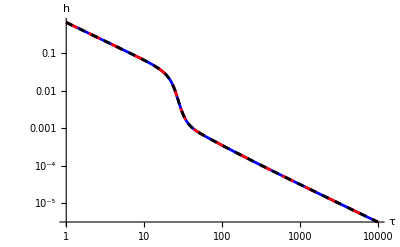

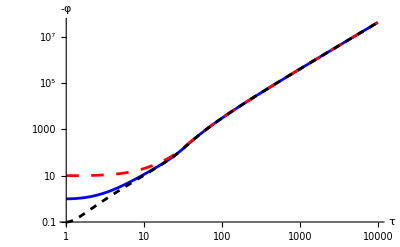

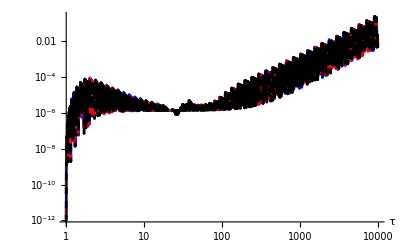

```mathematica
Params1db4={Δ->10^2,Γ->10^0,ϵ->1,α->11/10};
Params2db4={Δ->10^2,Γ->10^1,ϵ->1,α->11/10};
Params3db4={Δ->10^2,Γ->10^-1,ϵ->1,α->11/10};
Initdb4={h[δ]->2/(3δ),ψ[δ]->-Γ,ψ'[δ]->0,ϱ[δ]->3 Δ^2(2/(3δ))^2};

NSoldb4[params_,τ0_,τf_]:=NDSolve[{HeqTCdb4/.p->Function[τ,0],SeqTCdb4,MatEqdb4/.p->Function[τ,0],h[δ]==(h[δ]/.Initdb4),ψ[δ]==(ψ[δ]/.Initdb4),ψ'[δ]==(ψ'[δ]/.Initdb4),ϱ[δ]==(ϱ[δ]/.Initdb4)}/.params/.δ->τ0,{h,ψ,ϱ},{τ,δ,τf}/.δ->τ0,PrecisionGoal->10,WorkingPrecision->30]

nsol1=NSoldb4[Params1db4,1,10^4];
nsol2=NSoldb4[Params2db4,1,10^4];
nsol3=NSoldb4[Params3db4,1,10^4];

(* Hubble function *)
LogLogPlot[{h[τ]/.nsol1,h[τ]/.nsol2,h[τ]/.nsol3},{τ,1,10^4},PlotRange->All,PlotStyle->{{Thickness[0.005],Blue},{Thickness[0.005],Red,Dashing[Medium]},{Thickness[0.005],Black,Dashing[Small]}},AxesLabel->{"τ","h"},AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],Ticks->Automatic,TicksStyle->Directive[Black,15]]

(* scalar field *)
LogLogPlot[{-ψ[τ]/.nsol1,-ψ[τ]/.nsol2,-ψ[τ]/.nsol3},{τ,1,10^4},PlotRange->All,PlotStyle->{{Thickness[0.005],Blue},{Thickness[0.005],Red,Dashing[Medium]},{Thickness[0.005],Black,Dashing[Small]}},AxesLabel->{"τ","-φ"},AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],Ticks->Automatic,TicksStyle->Directive[Black,15]]

(* Hamiltonian constraint *)
LogLogPlot[{FeqTCdb4[[1]]-FeqTCdb4[[2]]/.Params1db4/.nsol1,FeqTCdb4[[1]]-FeqTCdb4[[2]]/.Params2db4/.nsol2,FeqTCdb4[[1]]-FeqTCdb4[[2]]/.Params3db4/.nsol3},{τ,1,10^4},PlotRange->All,PlotStyle->{{Thickness[0.005],Blue},{Thickness[0.005],Red,Dashing[Medium]},{Thickness[0.005],Black,Dashing[Small]}},AxesLabel->{"τ",""},AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],Ticks->Automatic,TicksStyle->Directive[Black,15]]
```

We can also plot the densities including matter in a single plot for one choice of theory parameters:

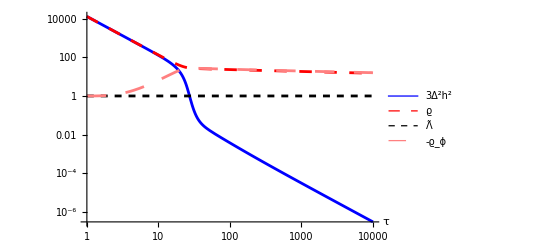

```mathematica
LogLogPlot[{3 Δ^2 h[τ]^2/.Params1db4/.nsol1,ϱ[τ]/.nsol1,Γ/.Params1db4,-(ψ[τ]+1/2 ϵ ψ'[τ]^2-3 α^3 ϵ^2 h[τ] ψ'[τ]^3)/.Params1db4/.nsol1},{τ,1,10^4},PlotRange->All,PlotStyle->{{Thickness[0.005],Blue},{Thickness[0.005],Red,Dashing[Medium]},{Thickness[0.005],Black,Dashing[Small]},{Thickness[0.005],Pink,Dashing[Large]}},AxesLabel->{"τ",""},AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],Ticks->Automatic,TicksStyle->Directive[Black,15],PlotLegends->{"3Δ^2h^2","ϱ","Λ̃","-ϱ_ϕ"}]
```

#### D. V~m^2 φ^2

In this section, we explore the degeneracy breaking by provided the scalar a bare mass m. The field equations become...

```mathematica
$Assumptions=λ≠0&&ϵ>0&&m≥0;

Vacuum={ρ->Function[t,0],P->Function[t,0]};
GoDimless={κ->λ/α,ℳ->λ Δ,Λ->Γ λ^4,H[t]->λ h[τ],H'[t]->λ^2 h'[τ],φ[t]->λ ψ[τ],φ'[t]->λ^2 ψ'[τ],φ''[t]->λ^3 ψ''[τ]};
db2={F->Function[x,0],V->Function[x,-(m^2 x^2)/2]};

FeqTCdb2=3 Δ^2 h[τ]^2==(3 Δ^2 hsq/.Solve[FeqTC/.M->0/.db2/.(NearlyBbm/.κ->λ)/.Vacuum/.GoDimless/.m->λ μ/.h[τ]^2->hsq,hsq][[1]]//Simplify);
HeqTCdb2=-2 Δ^2 h'[τ]==(-2 Δ^2 h'[τ]/.Solve[HeqTC/.M->0/.db2/.(NearlyBbm/.κ->λ)/.Vacuum/.GoDimless/.m->λ μ,h'[τ]][[1]]);
SeqTCdb2=0==ψ''[τ](ϵ-6 ϵ^2 h[τ]ψ'[τ])-(ψ''[τ](ϵ-6 ϵ^2 h[τ]ψ'[τ])/.Solve[SeqTC/.M->0/.db2/.(NearlyBbm/.κ->λ)/.Vacuum/.GoDimless/.m->λ μ//Simplify,ψ''[τ]][[1]]//Simplify);

FeqTCdb2
HeqTCdb2
SeqTCdb2
```

3 Δ^2 h[τ]^2==Γ+ψ[τ]+1/2 μ^2 ψ[τ]^2+1/2 ϵ ψ'[τ]^2-3 ϵ^2 h[τ] ψ'[τ]^3

-2 Δ^2 h'[τ]==ϵ ψ'[τ]^2-3 ϵ^2 h[τ] ψ'[τ]^3+ϵ^2 ψ'[τ]^2 ψ''[τ]

0==1+μ^2 ψ[τ]+3 ϵ h[τ] ψ'[τ]-9 ϵ^2 h[τ]^2 ψ'[τ]^2-3 ϵ^2 h'[τ] ψ'[τ]^2+(ϵ-6 ϵ^2 h[τ] ψ'[τ]) ψ''[τ]

We proceed numerically with Δ>>1, Γ~O(1),and μ~O(1).

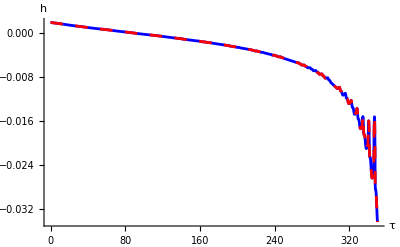

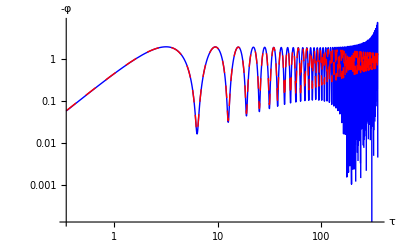

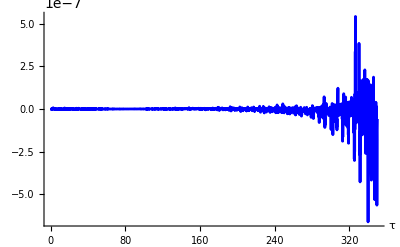

```mathematica
Paramsdb2={Δ->10^2,Γ->10^-1,μ->1,ϵ->1};
Initdb2={h[0]->√(Γ/(3 Δ^2)),ψ[0]->0,ψ'[0]->0};

nsol=NDSolve[{HeqTCdb2,SeqTCdb2,h[0]==(h[0]/.Initdb2),ψ[0]==(ψ[0]/.Initdb2),ψ'[0]==(ψ'[0]/.Initdb2)}/.Paramsdb2,{h,ψ},{τ,0,350},PrecisionGoal->10,WorkingPrecision->30];

δhdb2Approx=NDSolve[{2 Δ^2 δh'[τ]-3 ϵ^2 φ'[τ]^3 δh[τ]==-ϵ^2 φ'[τ]^2 φ''[τ]-ϵ φ'[τ]^2/.φ->Function[τ,ψ[τ]]/.nsol,δh[0]==(h[0]/.Initdb2)}/.Paramsdb2,δh,{τ,0,350},PrecisionGoal->10,WorkingPrecision->30];

(* Hubble function *)
Plot[{h[τ]/.nsol,δh[τ]/.δhdb2Approx},{τ,0,350},PlotRange->All,PlotStyle->{{Thickness[0.005],Blue},{Thickness[0.005],Red,Dashing[Medium]}},AxesLabel->{"τ","h"},AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],Ticks->Automatic,TicksStyle->Directive[Black,15]]

(* scalar field *)
ψsr[t_]=1/μ^2(E^(-3ϵ h[0]τ/2)Cos[(μ τ)/(√ϵ)]-1);
LogLogPlot[{-ψ[τ]/.nsol,-ψsr[τ]/.Initdb2/.Paramsdb2},{τ,0,350},PlotRange->All,PlotStyle->{{Thickness[0.0025],Blue},{Thickness[0.0025],Red,Dashing[Medium]}},AxesLabel->{"τ","-φ"},AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],Ticks->Automatic,TicksStyle->Directive[Black,15]]

(* Hamiltonian constraint *)
Plot[FeqTCdb2[[1]]-FeqTCdb2[[2]]/.Paramsdb2/.nsol,{τ,0,350},PlotRange->All,PlotStyle->{{Thickness[0.005],Blue},{Thickness[0.005],Red,Dashing[Medium]}},AxesLabel->{"τ",""},AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],Ticks->Automatic,TicksStyle->Directive[Black,15]]
```

With a different set of parameter values, we get...

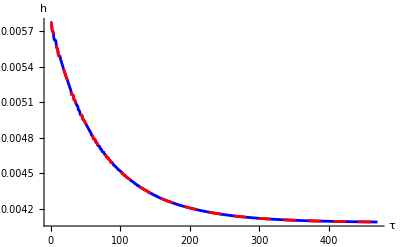

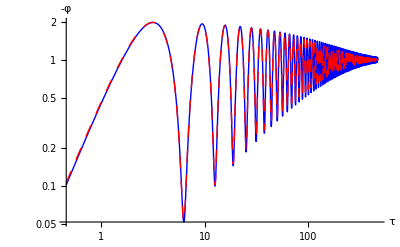

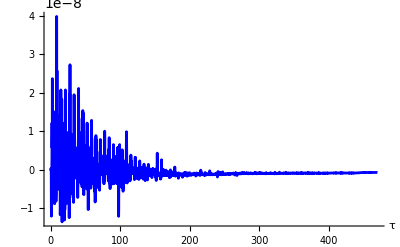

```mathematica
Paramsdb2={Δ->10^2,Γ->1,μ->1,ϵ->1};
Initdb2={h[0]->√(Γ/(3 Δ^2)),ψ[0]->0,ψ'[0]->0};

nsol=NDSolve[{HeqTCdb2,SeqTCdb2,h[0]==(h[0]/.Initdb2),ψ[0]==(ψ[0]/.Initdb2),ψ'[0]==(ψ'[0]/.Initdb2)}/.Paramsdb2,{h,ψ},{τ,0,470},PrecisionGoal->10,WorkingPrecision->30];

δhdb2Approx=NDSolve[{2 Δ^2 δh'[τ]-3 ϵ^2 φ'[τ]^3 δh[τ]==-ϵ^2 φ'[τ]^2 φ''[τ]-ϵ φ'[τ]^2/.φ->Function[τ,ψ[τ]]/.nsol,δh[0]==(h[0]/.Initdb2)}/.Paramsdb2,δh,{τ,0,470},PrecisionGoal->10,WorkingPrecision->30];

(* Hubble function *)
Plot[{h[τ]/.nsol,δh[τ]/.δhdb2Approx},{τ,0,470},PlotRange->All,PlotStyle->{{Thickness[0.005],Blue},{Thickness[0.005],Red,Dashing[Medium]}},AxesLabel->{"τ","h"},AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],Ticks->Automatic,TicksStyle->Directive[Black,15]]

(* scalar field *)
LogLogPlot[{-ψ[τ]/.nsol,-ψsr[τ]/.Initdb2/.Paramsdb2},{τ,0,470},PlotRange->All,PlotStyle->{{Thickness[0.0025],Blue},{Thickness[0.0025],Red,Dashing[Medium]}},AxesLabel->{"τ","-φ"},AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],Ticks->Automatic,TicksStyle->Directive[Black,15]]

(* Hamiltonian constraint *)
Plot[FeqTCdb2[[1]]-FeqTCdb2[[2]]/.Paramsdb2/.nsol,{τ,0,470},PlotRange->All,PlotStyle->{{Thickness[0.005],Blue},{Thickness[0.005],Red,Dashing[Medium]}},AxesLabel->{"τ",""},AxesStyle->Directive[Black,15],LabelStyle->Directive[Black,15],Ticks->Automatic,TicksStyle->Directive[Black,15]]
```

This is the end.